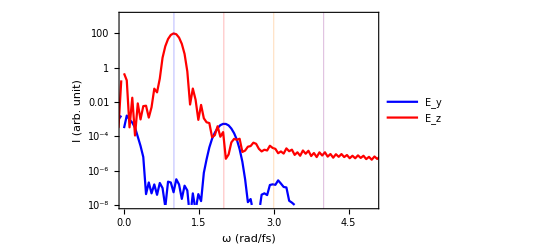

```mathematica
SetDirectory[NotebookDirectory[]];
(*Sacamos los datos crudos del programa: campo eléctrico en z y en y para todos los instantes de tiempo de la simulación para una posición dentro del medio no lineal dispersivo (wall+50). Vamos a calcular dentro de este fichero la transformada de Fourier para Ez y Ey. Representamos la intensidad espectral en escala logaritmica. En nuestro código la fuente puntual introduce un campo Ez en el vacío. Luego se propaga por el segundo medio, donde las polarizaciones no lineales están cruzadas y tienen contribución tanto de la polarización en y como en z. En este caso vemos como se genera una señal de segundo armónico para la componente en y, donde inicialmente no había señal. *)
datos=Import["datosTF.txt","Data"];
np=datos[[1,1]];
dt=datos[[1,2]];
tmax=np*dt;
dw=2*Pi/tmax;
wmax=Pi/dt;
wp=Table[(i-1)*dw,{i,1,np/2}];
wn=Table[-wmax+(i-1)*dw,{i,1,np/2}];
(*--------------------------Datos para Ez--------------------------------*)
wpulsoz=datos[[2,1]];
ezlist=datos[[Range[3,np+2],2]];
l2=Fourier[ezlist];
b=Re[l2*Conjugate[l2]];
puntosTFEz=ListPlot[b,PlotStyle->{RGBColor[0,0,1]},PlotRange->All,PlotLabel->"Datos TF del Ez"];
wez=Join[wp,wn]/wpulsoz;
wft1ez=Table[{wez[[i]],Re[l2[[i]]*Conjugate[l2[[i]]]]},{i,1,np}];
(*--------------------------Datos para Ey--------------------------------*)
eylist=datos[[Range[3,np+2],1]];
l1=Fourier[eylist];
a=Re[l1*Conjugate[l1]];
puntosTFEy=ListPlot[a,PlotStyle->{RGBColor[1,0,0]},PlotRange->All,PlotLabel->"Datos TF del Ey"];
wey=Join[wp,wn]/wpulsoz; (*La frecuencia está normalizada con respecto a la del pulso incidente. El pulso incide con el campo eléctrico orientado a lo largo del eje z*)
wft1ey=Table[{wey[[i]],Re[l1[[i]]*Conjugate[l1[[i]]]]},{i,1,np}];
(*--------------------------Espectro de Ez y Ey--------------------------------*)
ListLogPlot[{wft1ey,wft1ez},PlotRange->{{0,5},{10^3,0.00000001}},PlotStyle-> {RGBColor[0,0,1],RGBColor[1,0,0]},Joined->True,Frame->True,FrameLabel->{Style["ω (rad/fs)",16],Style["I (arb. unit)",16]," "," "},FrameStyle->{Black,Black,Black,Black},Axes->False,LabelStyle->{FontFamily->"Helvetica",FontSize->14},GridLines->{{{wpulsoz/wpulsoz,Directive[Blue]},{wpulsoz/wpulsoz*2,Directive[Red]},{wpulsoz/wpulsoz*3,Directive[Orange]},{wpulsoz/wpulsoz*4,Directive[Purple]}}, {0}}, PlotLegends->Placed[{"E_y","E_z"},{Scaled[{0.8,0.8}], {0, 0.8}}]]
```